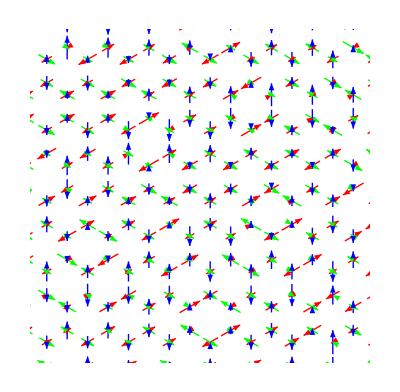

```mathematica
(*plot in original spin-coordinates*)
(*********************************************)
lenX=24;
lenY=24;
numCell=lenX lenY;
arrowWei=0.01;
spinLen=0.6;
colX=Red;
colY=Green;
colZ=Blue;
plotRange={{4.25,12.25},{1.1,8.95}};
dataLoc=StringJoin[NotebookDirectory[],"dataOut/conf.dat"];
(*********************************************)
coorToCode[coor_]:=1+coor[[1]]+coor[[2]] lenX+coor[[3]] numCell;
codeToCoor[code_]:=Module[{remain,coor1,coor2,coor3},remain=code-1;
coor3=Floor[remain/numCell];
remain=remain-coor3 numCell;
coor2=Floor[remain/lenX];
coor1=remain-coor2 lenX;
{coor1,coor2,coor3}];
uniX={1,0}//N;
uniY={1/2,(√3)/2}//N;
uniC={0,1/(√3)}//N;
vecRListA=Table[Module[{coorTemp},
coorTemp=codeToCoor[i];
coorTemp⟦1⟧uniX+coorTemp⟦2⟧uniY
],{i,1,numCell}];
vecRListB=Table[Module[{coorTemp},
coorTemp=codeToCoor[i+numCell];
coorTemp⟦1⟧uniX+coorTemp⟦2⟧uniY+uniC
],{i,1,numCell}];
vecRList=Join[vecRListA,vecRListB];

(*read data*)
data=Import[dataLoc];
locList=vecRList;
conf=data;
(*plot in original spin coordinates*)
arrowListX=Table[{colX,Arrowheads[arrowWei],Arrow[{
{locList⟦i,1⟧+(√3)/4 conf⟦i,1⟧spinLen,locList⟦i,2⟧+1/4 conf⟦i,1⟧spinLen},
{locList⟦i,1⟧-(√3)/4 conf⟦i,1⟧spinLen,locList⟦i,2⟧-1/4 conf⟦i,1⟧spinLen}
}]},{i,1,Length[conf]}];
arrowListY=Table[{colY,Arrowheads[arrowWei],Arrow[{
{locList⟦i,1⟧-(√3)/4 conf⟦i,2⟧spinLen,locList⟦i,2⟧+1/4 conf⟦i,2⟧spinLen},
{locList⟦i,1⟧+(√3)/4 conf⟦i,2⟧spinLen,locList⟦i,2⟧-1/4 conf⟦i,2⟧spinLen}
}]},{i,1,Length[conf]}];
arrowListZ=Table[{colZ,Arrowheads[arrowWei],Arrow[{
{locList⟦i,1⟧,locList⟦i,2⟧-1/2 conf⟦i,3⟧spinLen},
{locList⟦i,1⟧,locList⟦i,2⟧+1/2 conf⟦i,3⟧spinLen}
}]},{i,1,Length[conf]}];
arrowList=Join[arrowListX,arrowListY,arrowListZ];
gra=Graphics[arrowList,PlotRange->plotRange];
Export[StringJoin[NotebookDirectory[],"snapshot.eps"],gra];
Export[StringJoin[NotebookDirectory[],"snapshot.png"],gra];
Show[gra]
```

```mathematica
numCellX=lenX;
numCellY=lenY;
bondListX=Table[{
coorToCode[{xCoor,Mod[yCoor+1,numCellY],0}],
coorToCode[{xCoor,yCoor,1}]
},{xCoor,0,numCellX-1},{yCoor,0,numCellY-1}];
bondListX=Flatten[bondListX,1];
bondListY=Table[{
coorToCode[{Mod[xCoor-1,numCellX],Mod[yCoor+1,numCellY],0}],
coorToCode[{xCoor,yCoor,1}]
},{xCoor,0,numCellX-1},{yCoor,0,numCellY-1}];
bondListY=Flatten[bondListY,1];
bondListZ=Table[{
coorToCode[{xCoor,yCoor,0}],
coorToCode[{xCoor,yCoor,1}]
},{xCoor,0,numCellX-1},{yCoor,0,numCellY-1}];
bondListZ=Flatten[bondListZ,1];
bondList=Join[bondListX,bondListY,bondListZ];
confPlot=conf;
lineListA=Table[{
{x-confPlot⟦coorToCode[{x,y,0}],1⟧/2,y-confPlot⟦coorToCode[{x,y,0}],2⟧/2,-confPlot⟦coorToCode[{x,y,0}],3⟧/2},
{x+confPlot⟦coorToCode[{x,y,0}],1⟧/2,y+confPlot⟦coorToCode[{x,y,0}],2⟧/2,confPlot⟦coorToCode[{x,y,0}],3⟧/2}
},{x,0,numCellX-1},{y,0,numCellY-1}];
lineListA=Flatten[lineListA,1];
gA=Graphics3D[{Arrowheads[0.01],Arrow[Line[lineListA]]}];
lineListB=Table[{
{x-confPlot⟦coorToCode[{x,y,1}],1⟧/2,y-confPlot⟦coorToCode[{x,y,1}],2⟧/2,-confPlot⟦coorToCode[{x,y,1}],3⟧/2},
{x+confPlot⟦coorToCode[{x,y,1}],1⟧/2,y+confPlot⟦coorToCode[{x,y,1}],2⟧/2,confPlot⟦coorToCode[{x,y,1}],3⟧/2}
},{x,0,numCellX-1},{y,0,numCellY-1}];
lineListB=Flatten[lineListB,1];
gB=Graphics3D[{Arrowheads[0.01],Arrow[Line[lineListB]]}];
(*plot the confPlotiguration in a graphene lattice*)
(*unit vectors*)
uniX={1,0}//N;
uniY={1/2,(√3)/2}//N;
uniC={0,1/(√3)}//N;
(*create point list*)
pointListA=Table[xCoor uniX+yCoor uniY,{xCoor,0,lenX-1},{yCoor,0,lenY-1}];
pointListA=Flatten[pointListA,1];
pointListB=Table[xCoor uniX+yCoor uniY+uniC,{xCoor,0,lenX-1},{yCoor,0,lenY-1}];
pointListB=Flatten[pointListB,1];
pointList=Join[pointListA,pointListB];
(*create bond list*)
bondListA=Table[{xCoor uniX+yCoor uniY+uniC,xCoor uniX+(yCoor+1)uniY},{xCoor,0,lenX-1},{yCoor,0,lenY-1}];
bondListA=Flatten[bondListA,1];
bondListB=Table[{xCoor uniX+yCoor uniY+uniC,(xCoor-1) uniX+(yCoor+1)uniY},{xCoor,0,lenX-1},{yCoor,0,lenY-1}];
bondListB=Flatten[bondListB,1];
bondListC=Table[{xCoor uniX+yCoor uniY+uniC,xCoor uniX+yCoor uniY},{xCoor,0,lenX-1},{yCoor,0,lenY-1}];
bondListC=Flatten[bondListC,1];
bondList=Join[bondListA,bondListB,bondListC];
(*generate points in 3D*)
pointList=Table[{pointList⟦i,1⟧,pointList⟦i,2⟧,0.0},{i,1,Length[pointList]}];
graPoint=Graphics3D[{Point[pointList]}];
bondList=Table[{{bondList⟦i,1,1⟧,bondList⟦i,1,2⟧,0},{bondList⟦i,2,1⟧,bondList⟦i,2,2⟧,0}},{i,1,Length[bondList]}];
graBond=Graphics3D[{Line[bondList]}];
lineListA=Table[Module[{},
spin=confPlot⟦coorToCode[{x,y,0}]⟧;
pointInd=x numCellY+y+1;
point=pointList⟦pointInd⟧;
{
{point⟦1⟧-confPlot⟦coorToCode[{x,y,0}],1⟧/2,point⟦2⟧-confPlot⟦coorToCode[{x,y,0}],2⟧/2,-confPlot⟦coorToCode[{x,y,0}],3⟧/2},
{point⟦1⟧+confPlot⟦coorToCode[{x,y,0}],1⟧/2,point⟦2⟧+confPlot⟦coorToCode[{x,y,0}],2⟧/2,confPlot⟦coorToCode[{x,y,0}],3⟧/2}
}
],{x,0,numCellX-1},{y,0,numCellY-1}];
lineListA=Flatten[lineListA,1];
gA=Graphics3D[{Arrowheads[0.005],Blue,Arrow[Line[lineListA]]}];
lineListB=Table[Module[{},
spin=confPlot⟦coorToCode[{x,y,0}]⟧;
pointInd=x numCellY+y+1+numCell;
point=pointList⟦pointInd⟧;
{
{point⟦1⟧-confPlot⟦coorToCode[{x,y,1}],1⟧/2,point⟦2⟧-confPlot⟦coorToCode[{x,y,1}],2⟧/2,-confPlot⟦coorToCode[{x,y,1}],3⟧/2},
{point⟦1⟧+confPlot⟦coorToCode[{x,y,1}],1⟧/2,point⟦2⟧+confPlot⟦coorToCode[{x,y,1}],2⟧/2,confPlot⟦coorToCode[{x,y,1}],3⟧/2}
}
],{x,0,numCellX-1},{y,0,numCellY-1}];
lineListB=Flatten[lineListB,1];
gB=Graphics3D[{Arrowheads[0.005],Red,Arrow[Line[lineListB]]}];
gra3D=Show[graBond,graPoint,gA,gB,ImageSize->Full,ViewPoint->Top];
Export[StringJoin[NotebookDirectory[],"snapshot3D.eps"],gra3D];
Export[StringJoin[NotebookDirectory[],"snapshot3D.png"],gra3D];
Show[gra3D]
```

-Graphics3D-